```mathematica
(*Capacitante function parameters*)
SetDirectory[NotebookDirectory[]];
τ1 = 0.3;τ2 = 0.4;τ3 = 0.9;τ4 = 1;
C0=0.5;T=1; θ1=(1-C0)/(τ2-τ1);θ2=(1-C0)/(τ4-τ3);
(*FHN Parameters*)
ep=0.08;β=0.8;γ=0.7;maxtime=50;
Ct[t_]=Which[Mod[t,T]<τ1 T,1,Mod[t,T]<τ2,1-(Mod[t,T]-τ1 T)θ1, Mod[t,T]<τ3,C0, True,C0+(Mod[t,T]-T+(1-C0)/θ2)θ2];
Ctd[t_]=Which[Mod[t,T]<τ1 T,0,Mod[t,T]<τ2,-θ1, Mod[t,T]<τ3,0, True,θ2];
```

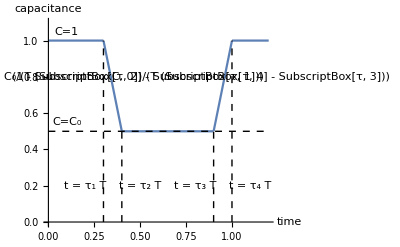

Fig1.png

```mathematica
CC[t_]=Which[t< τ1 T,1,t<τ2 T,1-(t- τ1 T) θ1,t<τ3 T,C0,True,C0 + (t-T+(1-C0)/θ2)θ2];
g1 = Plot[{CC[Mod[t,T]]},{t,0,1.2*T},PlotRange->{0,1.1},PlotLegends->Placed[StringJoin["C_0=",ToString[C0],", T=",ToString[T],", τ_1=",ToString[τ1],", τ_2=",ToString[τ2],", τ_3=",ToString[τ3],", τ_4=",ToString[τ4]],Above],AxesLabel->{"time","capacitance"}];
g2 = Graphics[{Dashed, Line[{{τ1 T,0},{τ1 T,1}}]}];
g3 = Graphics[{Text["t = τ_1 T",{τ1  T -0.1,0.2}]}];
g4 = Graphics[{Dashed, Line[{{τ2 T,0},{τ2 T,C0}}]}];
g5 = Graphics[{Text["t = τ_2 T",{τ2 T +0.1,0.2}]}];
g6 = Graphics[{Dashed, Line[{{τ3 T,0},{τ3 T,C0}}]}];
g7 = Graphics[{Text["t = τ_3 T",{τ3 T -0.1,0.2}]}];
g8 = Graphics[{Dashed, Line[{{τ4,0},{τ4,1}}]}];
g9 = Graphics[{Text["t = τ_4 T",{τ4 T+0.1,0.2}]}];

g10 = Graphics[{Text["C_0/(T (SubscriptBox[τ, 2] - SubscriptBox[τ, 1]))",{14/30*T,0.8}],Text["(1 - SubscriptBox[C, 0])/(T (SubscriptBox[τ, 4] - SubscriptBox[τ, 3]))",{25/30T,0.8}]}];
g11= Graphics[{Dashed, Line[{{0,C0},{1.2T,C0}}]}];
(*g11= Graphics[{Dashed, Line[{{0,C0},{τ2 T,C0}}]}];*)
g12 = Graphics[{Text["C=1",{0.1 T,1.05}]}];
g13 = Graphics[{Text["C=C_0",{0.1 T,0.55}]}];


export = Show[g1,g2,g3,g4,g5,g6,g7,g8,g9,g10,g11,g12,g13]
Export["Fig1.png",export]
```